```mathematica
(*
Original plot g=0.01

A.K.A. the USS 'The Mistake'
*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Zenth\Desktop\wtf

```mathematica
(*Folder="LKTesting";*)
Folder="T00_00.txt";
Sub="NoUVCut//lowg//";

Mu0Dat=ReadList["Mu0.txt",Number];
Mu1Dat=ReadList["Mu1.txt",Number];
h=0.02
Dim=Sqrt[Dimensions[Mu0Dat][[1]]]
```

0.02

1201

```mathematica
z=(Dim+1)/2;
Mu0=Table[{(x-z)*h,Mu0Dat[[(x-1)*Dim+z]]},{x,1,Dim}];
Mu1=Table[{(x-z)*h,Mu1Dat[[(x-1)*Dim+z]]},{x,1,Dim}];
```

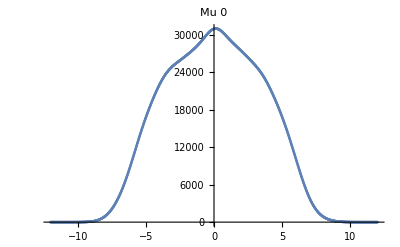

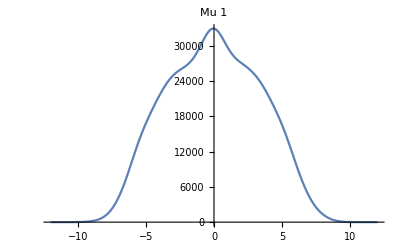

```mathematica
ListPlot[Mu0,PlotLabel->"Mu 0"]
ListPlot[Mu1,PlotLabel->"Mu 1",Joined->True]
```

```mathematica
Export["Mu0.png",%%]
Export["Mu1.png",%%]
```

Mu0.png

Mu1.png

```mathematica
z=(Dim+1)/2;
Mu03D=Flatten[Table[{(x-z)*h,(y-z)*h,
Mu0Dat[[(x-1)*Dim+y]]
},{x,1,Dim},{y,1,Dim}],1];
Mu13D=Flatten[Table[{(x-z)*h,(y-z)*h,
Mu1Dat[[(x-1)*Dim+y]]
},{x,1,Dim},{y,1,Dim}],1];
```

```mathematica
ListPlot3D[Mu03D,PlotRange->All]
ListPlot3D[Mu13D,PlotRange->All]
```

$Aborted

$Aborted

```mathematica
z
```

601

```mathematica
Sqrt[Dimensions[T03Dat]]
```

{1201}

```mathematica
size=100;
T03Cut=Table[
T03Dat[[(i-1)*Dim+j]]
,{i,z-size,z+size},{j,z-size,z+size}];
DimCut=Dimensions[T03Cut][[1]]
z2=(DimCut+1)/2



G=0;
Di=2*G+1;

T03CutGrain=Flatten[Table[{(x-z2)*h,(y-z2)*h,
Sign[-8*Sum[T03Cut[[i]][[j]],{i,x-G,x+G},{j,y-G,y+G}]]
},{x,G+1,DimCut-G,Di},{y,G+1,DimCut-G,Di}],1];


T03CutP=Flatten[Table[{(i-z2)*h,(j-z2)*h,
Sign[T03Cut[[i]][[j]]/(150*11)]
},{i,1,DimCut},{j,1,DimCut}],1]
ListDensityPlot[T03CutGrain,PlotRange->All,PlotLegends->Automatic,InterpolationOrder->0]
```

201

101

{{-2.,-2.,1},{-2.,-1.98,1},{-2.,-1.96,1},{-2.,-1.94,-1},{-2.,-1.92,-1},{-2.,-1.9,-1},{-2.,-1.88,-1},{-2.,-1.86,-1},{-2.,-1.84,-1},40383,{2.,1.84,1},{2.,1.86,1},{2.,1.88,1},{2.,1.9,1},{2.,1.92,-1},{2.,1.94,-1},{2.,1.96,1},{2.,1.98,1},{2.,2.,1}}
 |  |  |  |

-Graphics-

g=bad

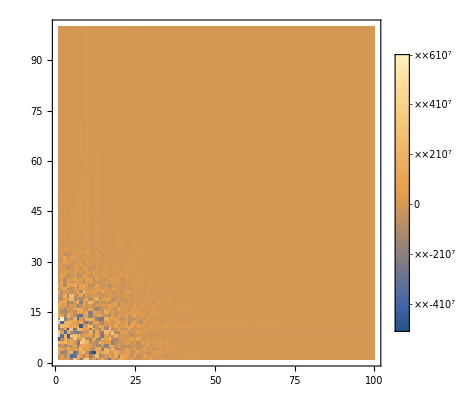

-Graphics3D-

```mathematica
FT03Cut=Fourier[T03Cut];


G=0;
Di=2*G+1;

FT03CutGrain=Flatten[Table[{x,y,
Sum[FT03Cut[[i]][[j]],{i,x-G,x+G},{j,y-G,y+G}]
},{x,G+1,(DimCut-G)/2,Di},{y,G+1,(DimCut-G)/2,Di}],1];


FT03CutP=Flatten[Table[{(i-z2)*h,(j-z2)*h,
Sign[FT03Cut[[i]][[j]]/(150*11)]
},{i,1,DimCut/4},{j,1,DimCut/4}],1];
ListDensityPlot[Re[FT03CutGrain],PlotRange->All,PlotLegends->Automatic,InterpolationOrder->0]
ListPlot3D[Re[FT03CutGrain],PlotRange->All,PlotLegends->Automatic]
```

{{7640.83+0. ⅈ,-7.94392×10^6-1.66535×10^6 ⅈ,1.20645×10^7+5.04268×10^6 ⅈ,1.25774×10^7+1.2381×10^7 ⅈ,94,278462.+11836.2 ⅈ,278480.+7091.86 ⅈ,278479.+2368.65 ⅈ},99,{1}}
 |  |  |  |

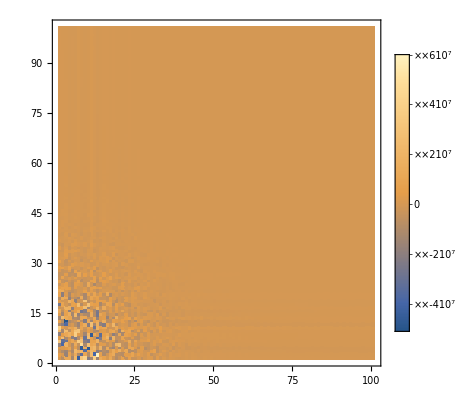

```mathematica
FT03CutGrain=Table[Sum[FT03Cut[[i]][[j]],{i,x-G,x+G},{j,y-G,y+G}],{x,G+1,(DimCut+1)/2},{y,G+1,(DimCut+1)/2}]
ListDensityPlot[Re[FT03CutGrain],PlotRange->All,PlotLegends->Automatic,InterpolationOrder->0]
```

```mathematica
Dimensions[FT03CutGrain]
Tot=Sum[Abs[FT03CutGrain[[i]][[j]]]^1,{i,1,(DimCut+1)/2},{j,1,(DimCut+1)/2}];
Sum[Sqrt[(i-1)^2+(j-1)^2]*Abs[FT03CutGrain[[i]][[j]]]^1/Tot,{i,1,(DimCut+1)/2},{j,1,(DimCut+1)/2}]
```

{101,101}

22.9852

```mathematica
DimCut
```

201

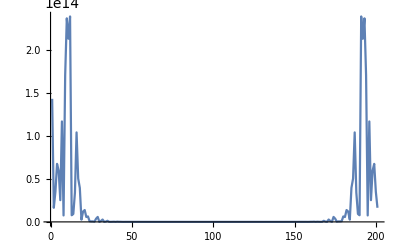

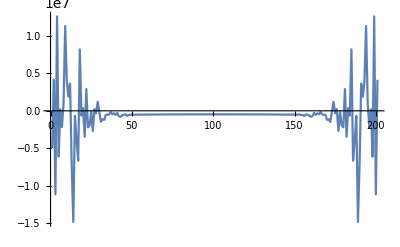

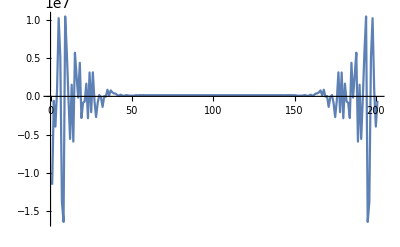

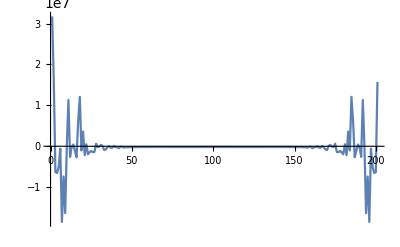

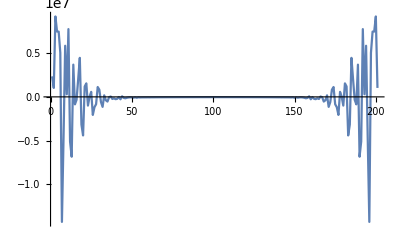

```mathematica
zspace=(z2-1)/2;
FourStrips=Table[Fourier[T03Cut[[All,z2+i*zspace]]]
,{i,-2,2}];

ListPlot[Re[FourStrips[[1]]]^2+Im[FourStrips[[1]]]^2,Joined->True,PlotRange->All]
ListPlot[Re[FourStrips[[2]]],Joined->True,PlotRange->All]
ListPlot[Re[FourStrips[[3]]],Joined->True,PlotRange->All]
ListPlot[Re[FourStrips[[4]]],Joined->True,PlotRange->All]
ListPlot[Re[FourStrips[[5]]],Joined->True,PlotRange->All]
```

```mathematica
FourTable=Table[Fourier[T03Cut[[All,i]]]
,{i,1,DimCut}];

For[j=1,j≤DimCut,j++,
FourTable[[1]][[j]]=Abs[FourTable[[1]][[j]]]^2;
]

For[i=2,i≤DimCut,i++,
For[j=1,j≤DimCut,j++,
FourTable[[1]][[j]]=FourTable[[1]][[j]]+Abs[FourTable[[i]][[j]]]^2;
]
]
```

```mathematica
ListPlot[FourTable[[1]],Joined->True,PlotRange->{{0,40},All}]
```

-Graphics-

```mathematica
ListDensityPlot[FourStrips,PlotRange->All,PlotLegends->Automatic,InterpolationOrder->0]
```

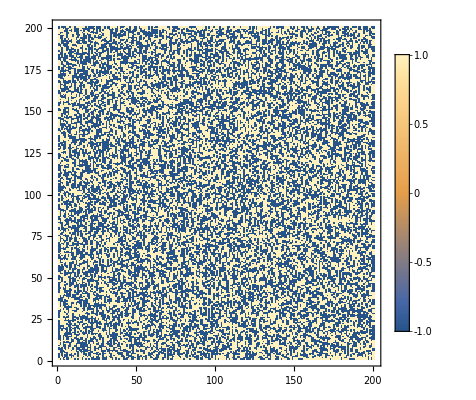

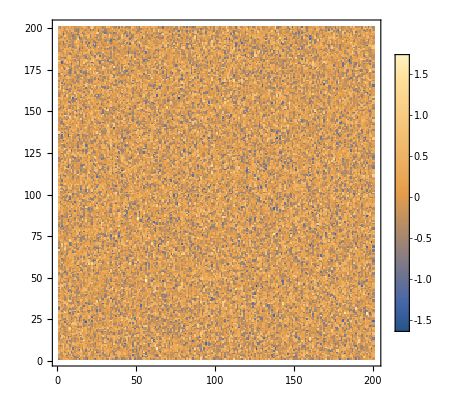

```mathematica
Noise=Table[2*RandomReal[]-1,{x,1,1201},{y,1,1201}];
ListDensityPlot[Sign[Re[Noise]],PlotRange->All,PlotLegends->Automatic,InterpolationOrder->0]
FTNoise=Fourier[Noise];
ListDensityPlot[Re[FTNoise],PlotRange->All,PlotLegends->Automatic,InterpolationOrder->0]
```

```mathematica
Noise=Table[2*RandomReal[]-1,{x,1,1201},{y,1,1201}];
FNoise=Fourier[Noise]
```

{{0.177388-9.46601×10^-17 ⅈ,0.262869+0.0951916 ⅈ,-0.280446+0.203683 ⅈ,-0.500776+0.200421 ⅈ,1194,-0.500776-0.200421 ⅈ,-0.280446-0.203683 ⅈ,0.262869-0.0951916 ⅈ},1199,{1}}
 |  |  |  |

```mathematica
TNoise=Table[0,{x,1,1201},{y,1,1201}]
```

{1}
 |  |  |  |

```mathematica
InverseFourier[TNoise]
```

{{-0.0124828-1.1093×10^-18 ⅈ,-0.0129076+2.95813×10^-18 ⅈ,-0.0133235+3.69766×10^-18 ⅈ,1195,-0.0111611-2.2186×10^-18 ⅈ,-0.0116089+1.47906×10^-18 ⅈ,-0.0120497+3.69766×10^-19 ⅈ},1199,{1}}
 |  |  |  |

```mathematica
For[x=1,x≤11,x++,
For[y=1,y≤11,y++,
TNoise[[x]][[y]]=FNoise[[x]][[y]];
]
For[y=1201-9,y≤1201,y++,
TNoise[[x]][[y]]=FNoise[[x]][[y]];
]
]
For[x=1201-9,x≤1201,x++,
For[y=1,y≤11,y++,
TNoise[[x]][[y]]=FNoise[[x]][[y]];
]
For[y=1201-9,y≤1201,y++,
TNoise[[x]][[y]]=FNoise[[x]][[y]];
]
]
```

```mathematica
TNoise
```

{{0.177388-9.46601×10^-17 ⅈ,0.262869+0.0951916 ⅈ,-0.280446+0.203683 ⅈ,-0.500776+0.200421 ⅈ,1194,-0.500776-0.200421 ⅈ,-0.280446-0.203683 ⅈ,0.262869-0.0951916 ⅈ},1199,{1}}
 |  |  |  |

```mathematica
CutNoise=InverseFourier[TNoise];
```

```mathematica
SignNoise=Table[{x,y,Sign[Re[CutNoise[[x]][[y]]]]},{x,1,1201},{y,1,1201}]
```

{1}
 |  |  |  |

```mathematica
ListDensityPlot[SignNoise]
```

-Graphics-

```mathematica
SparseArray
```

Transform

{10,0,0,0,0,0,0,0,0,0,0,0}

Into

{2.88675,2.88675,2.88675,2.88675,2.88675,2.88675,2.88675,2.88675,2.88675,2.88675,2.88675,2.88675}

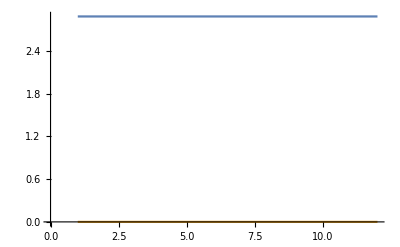

Transform

{0,10,0,0,0,0,0,0,0,0,0,0}

Into

{2.88675+0. ⅈ,2.5+1.44338 ⅈ,1.44338+2.5 ⅈ,0.+2.88675 ⅈ,-1.44338+2.5 ⅈ,-2.5+1.44338 ⅈ,-2.88675+0. ⅈ,-2.5-1.44338 ⅈ,-1.44338-2.5 ⅈ,0.-2.88675 ⅈ,1.44338-2.5 ⅈ,2.5-1.44338 ⅈ}

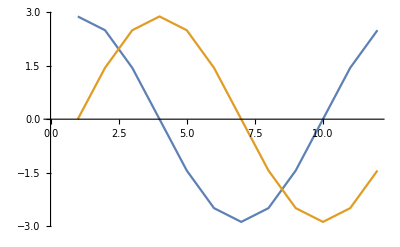

Transform

{0,0,0,0,0,0,0,0,0,0,0,10}

Into

{2.88675+0. ⅈ,2.5-1.44338 ⅈ,1.44338-2.5 ⅈ,0.-2.88675 ⅈ,-1.44338-2.5 ⅈ,-2.5-1.44338 ⅈ,-2.88675+0. ⅈ,-2.5+1.44338 ⅈ,-1.44338+2.5 ⅈ,0.+2.88675 ⅈ,1.44338+2.5 ⅈ,2.5+1.44338 ⅈ}

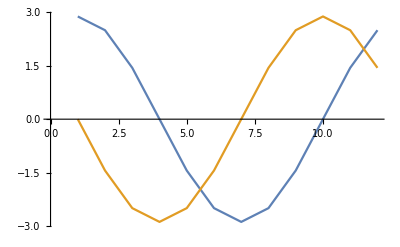

```mathematica
Print["Transform"]
This={10,0,0,0,0,0,0,0,0,0,0,0}
Print["Into"]
Test1=Fourier[This]
ListPlot[{Re[Test1],Im[Test1]},Joined->True]

Print["Transform"]
This={0,10,0,0,0,0,0,0,0,0,0,0}
Print["Into"]
Test1=Fourier[This]
ListPlot[{Re[Test1],Im[Test1]},Joined->True]

Print["Transform"]
This={0,0,0,0,0,0,0,0,0,0,0,10}
Print["Into"]
Test1=Fourier[This]
ListPlot[{Re[Test1],Im[Test1]},Joined->True]
```

{(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0,1/2,(√3)/2,1}

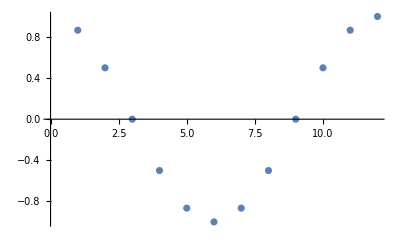

0.450905

```mathematica
Index=12;
ThisOther=Table[Cos[2*i*(Index-1)*Pi/12],{i,1,12}]
ListPlot[ThisOther]
```

Transform

{10,10,10,10,10,10,10,10,10,10,10,10}

Into

{34.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

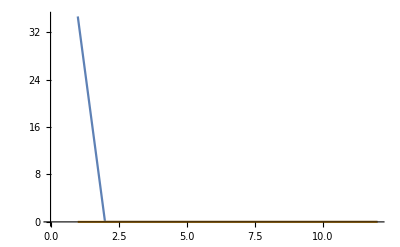

```mathematica
Print["Transform"]
This={10,10,10,10,10,10,10,10,10,10,10,10}
Print["Into"]
Test1=Fourier[This]
ListPlot[{Re[Test1],Im[Test1]},Joined->True]
```

```mathematica
Folder="SingleRun";
T00SDat=ReadList[Folder<>"//T00_00.txt",Number];
M0SDat=ReadList[Folder<>"//Mu0.txt",Number]
M1SDat=ReadList[Folder<>"//Mu1.txt",Number]
R0SDat=ReadList[Folder<>"//RhoAv0.txt",Number];
R1SDat=ReadList[Folder<>"//RhoAv1.txt",Number];
α0SDat=ReadList[Folder<>"//AlphaAv0.txt",Number];
α1SDat=ReadList[Folder<>"//AlphaAv1.txt",Number];
AxSDat=ReadList[Folder<>"//AxOffCor.txt",Number];
AySDat=ReadList[Folder<>"//AyOffCor.txt",Number];
h=0.02
```

{8.21614×10^-45,1.15544×10^-44,1.62375×10^-44,2.28024×10^-44,3.19983×10^-44,4.48701×10^-44,6.28734×10^-44,8.80347×10^-44,1.23173×10^-43,1.72207×10^-43,2.40579×10^-43,3.35841×10^-43,4.68466×10^-43,6.52963×10^-43,9.0942×10^-43,1.26562×10^-42,1.75998×10^-42,2.44552×10^-42,3.39545×10^-42,4.71069×10^-42,6.53025×10^-42,9.04555×10^-42,1.25198×10^-41,1.73149×10^-41,2.39276×10^-41,3.30395×10^-41,4.55854×10^-41,6.28455×10^-41,8.65722×10^-41,1.19162×10^-40,1.6389×10^-40,2.25228×10^-40,3.09277×10^-40,4.24352×10^-40,1442333,1.89091×10^-41,1.46767×10^-41,1.13826×10^-41,8.82073×10^-42,6.83×10^-42,5.28432×10^-42,4.08518×10^-42,3.15562×10^-42,2.43563×10^-42,1.87841×10^-42,1.44751×10^-42,1.11457×10^-42,8.57517×10^-43,6.59222×10^-43,5.06377×10^-43,3.88659×10^-43,2.98068×10^-43,2.2841×10^-43,1.74891×10^-43,1.33805×10^-43,1.02289×10^-43,7.81337×10^-44,5.9635×10^-44,4.54795×10^-44,3.46564×10^-44,2.63878×10^-44,2.0076×10^-44,1.52616×10^-44,1.15926×10^-44,8.79852×10^-45,6.67256×10^-45,5.05624×10^-45,3.82839×10^-45,2.89639×10^-45}
 |  |  |  |

{9.79771×10^-46,1.32909×10^-45,1.80152×10^-45,2.43991×10^-45,3.30188×10^-45,4.4648×10^-45,6.03248×10^-45,8.14407×10^-45,1.0986×10^-44,1.48078×10^-44,1.99432×10^-44,2.6838×10^-44,3.60877×10^-44,4.84864×10^-44,6.5093×10^-44,8.73173×10^-44,1.17036×10^-43,1.56744×10^-43,2.09756×10^-43,2.80473×10^-43,3.74732×10^-43,5.00267×10^-43,6.67324×10^-43,8.89454×10^-43,1.18458×10^-42,1.57636×10^-42,2.09604×10^-42,2.78482×10^-42,3.69697×10^-42,4.90398×10^-42,6.49985×10^-42,8.60817×10^-42,1.13912×10^-41,1.5062×10^-41,1442333,2.24226×10^-35,1.87261×10^-35,1.56268×10^-35,1.30304×10^-35,1.0857×10^-35,9.03904×10^-36,7.51964×10^-36,6.25075×10^-36,5.19192×10^-36,4.30907×10^-36,3.57354×10^-36,2.96123×10^-36,2.45191×10^-36,2.0286×10^-36,1.67704×10^-36,1.38532×10^-36,1.14344×10^-36,9.43046×10^-37,7.77158×10^-37,6.39945×10^-37,5.2654×10^-37,4.32889×10^-37,3.55612×10^-37,2.91899×10^-37,2.39411×10^-37,1.96205×10^-37,1.60669×10^-37,1.31465×10^-37,1.07483×10^-37,8.78065×10^-38,7.16749×10^-38,5.84605×10^-38,4.76443×10^-38,3.87985×10^-38}
 |  |  |  |

0.02

```mathematica
G=10;
Di=2*G+1;
z=(Dim+1)/2;
T00Sing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[T00SDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
M0Sing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[M0SDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
M1Sing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[M1SDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
R0Sing=Flatten[Table[{(x-z)*h,(y-z)*h,
Abs[Sum[R0SDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
R1Sing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[R1SDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
α0Sing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[α0SDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
α1Sing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[α1SDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
AxSing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[AxSDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
AySing=Flatten[Table[{(x-z)*h,(y-z)*h,
Sum[AySDat[[(i-1)*Dim+j]],{i,x-G,x+G},{j,y-G,y+G}]/((2*G+1)^2)
},{x,G+1,Dim-G,Di},{y,G+1,Dim-G,Di}],1];
```

```mathematica
Print["Nucleus 0"]
ListPlot3D[M0Sing,PlotRange->All,PlotLabel->"μ0"]
ListPlot3D[R0Sing,PlotRange->All,PlotLabel->"ρ0"]
ListPlot3D[α0Sing,PlotRange->All,PlotLabel->"α0"]
ListPlot3D[AxSing,PlotRange->All,PlotLabel->"Ax"]
ListPlot3D[AySing,PlotRange->All,PlotLabel->"Ay"]
ListPlot3D[T00Sing,PlotRange->All,PlotLabel->"T00"]

Print["Nucleus 1"]
ListPlot3D[M1Sing,PlotRange->All,PlotLabel->"μ1"]
ListPlot3D[R1Sing,PlotRange->All,PlotLabel->"ρ1"]
ListPlot3D[α1Sing,PlotRange->All,PlotLabel->"α1"]
ListPlot3D[AxSing,PlotRange->All,PlotLabel->"Ax"]
ListPlot3D[AySing,PlotRange->All,PlotLabel->"Ay"]
ListPlot3D[T00Sing,PlotRange->All,PlotLabel->"T00"]
```

Nucleus 0

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

Nucleus 1

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
Test2=Table[i+2*j,{i,0,5},{j,0,5}]
```

{{0,2,4,6,8,10},{1,3,5,7,9,11},{2,4,6,8,10,12},{3,5,7,9,11,13},{4,6,8,10,12,14},{5,7,9,11,13,15}}

```mathematica
Test2[[]][[1]]
```

{0,2,4,6,8,10}

```mathematica
Dimensions[Test2]
```

{6,6}

```mathematica
Test2[[All,1]]
```

{0,1,2,3,4,5}

```mathematica
(1/6)*Sqrt[2]*49*.2
```

2.30988